Вариант 8 (По определению)
1.

```mathematica
X={π/6,π/4,π/3,π/2};
f[x_]=Cot[x]^2;
n=Length[X]-1;
Do[{Subscript[x, i]=X[[i+1]], Subscript[f, i]=f[Subscript[x, i]]}, {i, 0, n}]
```

2.Строим алгебраический интерполяционный многочлен через определитель

```mathematica
Unprotect[Power];
0^0:=1;
Do[Subscript[fi, j][x_]=x^j,{j,0,n}];
Do[Subscript[d, i,j]=Subscript[fi, j][Subscript[x, i]],{i,0,n},{j,0,n}];
Do[{Subscript[d, i,n+1]=Subscript[f, i],Subscript[d, n+1,i]=Subscript[fi, i][x]},{i,0,n}];
Subscript[d, n+1,n+1]=0;
V=Table[Subscript[d, i,j],{i,0,n},{j,0,n}];
V1=Table[Subscript[d, i,j],{i,0,n+1},{j,0,n+1}];
%//MatrixForm
P[x_]=-Det[V1]/Det[V]//Expand
```

(1 | π/6 | π^2/36 | π^3/216 | 3
1 | π/4 | π^2/16 | π^3/64 | 1
1 | π/3 | π^2/9 | π^3/27 | 1/3
1 | π/2 | π^2/4 | π^3/8 | 0
1 | x | x^2 | x^3 | 0)

14-(103 x)/π+(258 x^2)/π^2-(216 x^3)/π^3

2.) Строим интерполционный многочлен с помощью встроенной функции InterpolatingPolynomial;

```mathematica
Tb1=Table[{Subscript[x, i],Subscript[f, i]},{i, 0, n}];
P1[x_]=InterpolatingPolynomial[Tb1, x]//Expand
```

3.)Проверяем многочлены

```mathematica
((P[x]-P1[x])//Chop)==0
```

True

4)Изобразить исходную систему точек

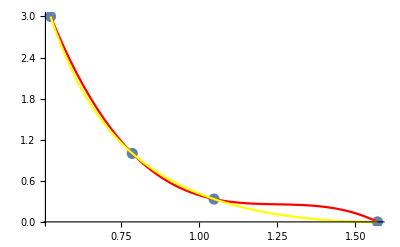

```mathematica
Gr1=ListPlot[Tb1,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x], {x, Subscript[x, 0], Subscript[x, n]},PlotStyle->Red];
Gr3=Plot[f[x], {x, Subscript[x, 0], Subscript[x, n]},PlotStyle-> Yellow];
Show[Gr1, Gr2, Gr3]
```

4) Найти приближенное значение f (x) при указанном аргументе.

```mathematica
SuperStar[x]=Pi/5;
P[SuperStar[x]]//N
A=N[Abs[f[SuperStar[x]]-P[SuperStar[x]]],2]
B=N[A/(P[SuperStar[x]]//Abs)100,2]
```

1.992

0.098

4.9

Задание 2. Доказать Утверждение, что на отрезке [2,b], b>2, система функций x,x^2,x^3,...,x^n Образует систему Чебышева, а на отрезке [-b,b] Не является чебышевской

Рассматриваемая система имеет n функций. Составляем обобщенный многочлен по заданной системе, он имеет вид
x( ∑_(i=0)^(n-1) a_i*x^i) .На отрезке [2,b] b>2 первый множитель не обращается в нуль, то есть корней не имеет. Второй множитель имеет не более чем n-1 корней, в результате все произведение имеет не больше чем n-1 корней на отрезке [2,b] b>2. По определению это означает что данная система является Чебышевской на [2,b] b>2.
Рассмотрим отрезок [-b,b]. 
x( ∑_(i=0)^(n-1) a_i*x^i).На отрезке [-b,b]  первый множитель имеет 1 корень. Второй множитель имеет более чем n-1 корней, в результате все произведение имеет  не более чем n корней на отрезке [-b,b] По определению это означает что данная система не является Чебышевской на [-b,b].